Complete The Wolfram Expression

Baschieri Daniele

Di Virgilio Riccardo

University of Bologna.

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: Design an interactive browser game where you can improve your skill with wolfram language, starting from a topic of your interest the system will show you a Wolfram Expression with a missing part to complete, in a growing of difficulty and fun.

SUMMARY OF WORK: Developing a web application based on Wolfram’s stack technology, focusing on exploring safe examples for the game in a dynamic self configuring context.
Application is ready for a public deployment, but with such a vast number of example more test are required to verify the stability of this alpha release.

RESULTS AND FUTURE  WORK: Application is now available in alpha stage on this link https://wolfr.am/complete-the-function the very next step is the releasing it on the WolframCloud and let it available for everyone. The gamification aspect of the application is really minimal right now, in the future could be useful add badges and karma-point in order to increase the fun and also adding multiple choice in the easy mode in order to balance the difficulty.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

The game is fully developed in Wolfram Mathematica Language, is composed with 3 different component:
The URLDispatcher redirect each http request on the correspondent template, it’s the entry point of the game and the most important part of the application.

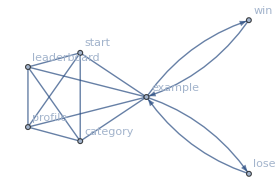

Current graph of the web page that URLDispatcher manage to present.

The second most important aspect of the game is the function that tweak a working wolfram expression and replace a Symbol with a Placeholder. (  1  )

```mathematica
Table[PieChart[{1,2,3},SectorOrigin->θ],{θ,{0,π/4,π/2}}]
```

```mathematica
Table[1[{1,2,3},SectorOrigin->θ],{θ,{0,π/4,π/2}}]
```

During this process is important to pay attention that the expression not evaluate, some Head like Now can produce different output if are not manage correctly.
Finally another section of this project is related with the classification of the exercise and the realization of a subset of instruction that can be used during the game.
Some Expression can be really dangerous for Wolfram Kernel. Expressions like Quit or Import, Export can compromise the Wolfram’s account of the user, so the system is designed to accept only a huge subset of expression and will present only the example form the documentation that contain expression in that’s safe subset.

-Graphics-

The best way to understand better the system is trying it at https://wolfr.am/complete-the-function

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

Code

The full source code can be found on GitHub

https://github.com/DangerBlack/WSS17-personal-project/tree/master/Project

The structure of the source code is quiet simple.
In order to run the code you need to use this instruction.

```mathematica
Unprotect[$TemplatePath];
$TemplatePath=Prepend[
					$TemplatePath,
					PacletManager`PacletResource["Project","Assets"]
					];
<<HTTPHandling`
<<Project`
StartWebServer[$CompleteExpressionApp]
```

Code is in the root of the Project folder, in different files:
core.m, whitelist.m are class related with the expression manipulation and retrieval from documentation.
category.m is the class with the accepted Symbols divided by categories.
webview.m is the dispatcher and the entry point of the whole application.
storage.m and settings.m are classes related with saving score in cloud and saving and loading data from the webserver’s machine.

Written Content / Lesson Plans

### Smart use of seed in Random

The development of the web interface leads to a series of trouble in making rest web resources for the clients.
When a user connect to a specific game the random symbol removed must be always the same, in order to accomplish this we encode the seed of the tweak function in the url.
When an user request a new exercises http://$AppRoot/category/BasicSymbols/easy/  the system generate a new list containing a list made by 
difficulty seed exerciseId hash 
than redirect the user to a different url,
for example:
http://$AppRoot/category/BasicSymbols/easy:294:10uwnetq30jhf:1j5e7hz091u8wyhllpctx5q3n04rxsm87l087qfowcxu00qjgo/
We design this system to keep integrity in the request made by the users, but we add the hash of the first tree values in the end in order to prevent that a user can manipulate the random seed and move the missing part and be able to discover the correct answer.

```mathematica
$uuid= "secret string stored in the server";
customHash[expr_,rest___]:=IntegerString[Hash[{expr,$uuid},rest],36]
signList[s_List]:=With[{l=Map[ToString,s]},StringJoin[Riffle[Append[l,customHash[l,"SHA256"]],":"]]]
unsign[{l__,h_}]:=If[MatchQ[customHash[{l},"SHA256"],h],{l},$Failed]
unsign[s_String]:=unsign[StringSplit[s,":"]]
unsign[__]:=$Failed
s=signList[{"easy",294,"10uwnetq30jhf"}]
unsign [s]
```

easy:294:10uwnetq30jhf:4jww2nqwqvud5jtu7r2mkepojfzbq0dwd8uebxo7zfzjqrp9zk

{easy,294,10uwnetq30jhf}

```mathematica
(* if we try to manipulate the seed in order to tweak different expression*)
unsign["easy:42:10uwnetq30jhf:4jww2nqwqvud5jtu7r2mkepojfzbq0dwd8uebxo7zfzjqrp9zk"]
```

$Failed

Conclusions in Detail

All Visualizations

Data Sources Links/References

Future Directions

Background Info Links/References

Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

Other

Date

Last Modified: Monday, July 03, 2017

```mathematica
"Add Timestamp"
```